Evaluation>Evaluate Notebook

```mathematica
$H="/Volumes/World/Users/latur/Public/DREAM6/r-code/";
FN[pattern_]:=FileNames[pattern,$H<>"results/",2];
```

```mathematica
(* Чтение файла известных параметров, преобразование в список *)
P=StringCases[
StringReplace[Import[#],"\n"->","],
RegularExpression["=([0-9.]{1,10})"]->"$1"
]&/@FileNames["parms.txt",$H,∞]//ToExpression;
```

```mathematica
(* График значений функционала *)
FValue[list_]:={#⟦1⟧,#⟦3⟧}&/@list;
```

```mathematica
(* График значений расстояния между параметрами *)
Distance[pred_,real_]:=Total[Log[pred/real⟦1;;Length[pred]⟧]^2]/Length[pred];
PValue[list_,p_]:={#⟦1⟧,Distance[#⟦4;;-1⟧,p]}&/@list;
```

```mathematica
LP[list_,prange_]:=ListPlot[ list,Frame->True,Mesh->All,Joined->True,PlotRange->prange,ImageSize->{250,180}];
Vi[e_,p_]:=Grid[{{LP[FValue/@e,{{-10,800},{-10,250}}],LP[PValue[#,p]&/@e,{{-10,900},{-1,10}}]}}];
```

Структура имён файлов: m1p150e2, m1 — модель (1), p150 — размер популяции (150), e2 — es_lambda (2)

```mathematica
MOO={#[[-1,3]]&/@(Import/@FN["*m1p150e2*.dev"]),#[[-1,3]]&/@(Import/@FN["*m1p150e15*.dev"]),#[[-1,3]]&/@(Import/@FN["*m1p150e45*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p150e2*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p150e15*.dev"]),#[[-1,3]]&/@(Import/@FN["*m2p150e45*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p150e2*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p150e15*.dev"]),#[[-1,3]]&/@(Import/@FN["*m3p150e45*.dev"])};
```

```mathematica
(* Приведение к латех-форме *)
η=Partition[Mean/@MOO,3];
φ=Partition[Min/@MOO,3];
β={η⟦1⟧,φ⟦1⟧,η⟦2⟧,φ⟦2⟧,η⟦3⟧,φ⟦3⟧}//Transpose;
StringReplace[β//ToString,{"}, {"->"\n",", "->" & ","{{"->"","}}"->""}]
```

49.3667 & 25.4139 & 22.8473 & 12.1157 & 48.6207 & 35.7457
44.0293 & 30.755 & 25.8365 & 12.1114 & 49.8181 & 30.1344
44.3788 & 24.9287 & 24.1793 & 15.0964 & 44.8327 & 34.6884

#### Размер популяции (150) фиксирован, es_lambda = 2, 15, 45.

```mathematica
tmp={
Import/@FN["*m1p150e2*.dev"],
Import/@FN["*m1p150e15*.dev"],
Import/@FN["*m1p150e45*.dev"],
Import/@FN["*m2p150e2*.dev"],
Import/@FN["*m2p150e15*.dev"],
Import/@FN["*m2p150e45*.dev"],
Import/@FN["*m3p150e2*.dev"],
Import/@FN["*m3p150e15*.dev"],
Import/@FN["*m3p150e45*.dev"]
};
```

```mathematica
plots=LP[FValue/@(#),{{-10,850},{-10,270}}]&/@tmp;
grid=Partition[plots,3]//Transpose//Grid
```

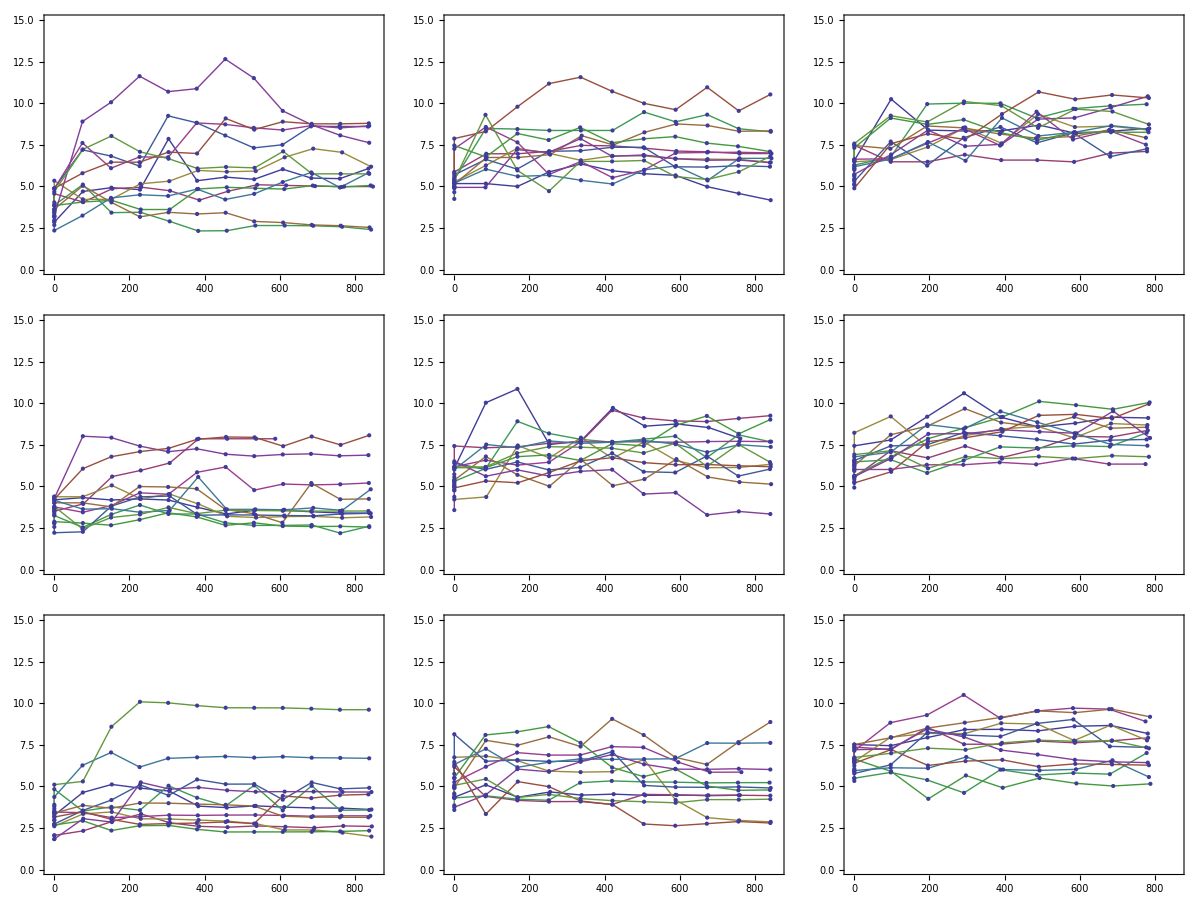

```mathematica
pplots=Table[LP[PValue[#,P⟦Round[(i+1)*3/9]⟧]&/@tmp⟦i⟧,{{-10,860},{0,15}}],{i,1,9}];
grid=Partition[pplots,3]//Transpose//Grid
```

```mathematica
Export["p150e.png",grid]
```

p150e.png

#### Лучшие значения:

```mathematica
m1={#⟦-1,3⟧,#⟦-1,4;;-1⟧}&/@(Import/@FN["results/*m1*.dev"])//Sort;
m2={#⟦-1,3⟧,#⟦-1,4;;-1⟧}&/@(Import/@FN["results/*m2*.dev"])//Sort;
m3={#⟦-1,3⟧,#⟦-1,4;;-1⟧}&/@(Import/@FN["results/*m3*.dev"])//Sort;
```

```mathematica
Fparams[file_,data_]:=Module[
{e=Import[file,"List"],f},
f=StringReplace[e⟦#⟧,RegularExpression["\=[0-9.]{1,10}"]->"="<>ToString[data⟦#⟧]<>"\n"]&/@Range[Length[e]];
Export[file<>".min",StringJoin[f],"Text"]];
```

```mathematica
(* Сохраниение в файл для получения таблицы концентраций *)
Fparams[$H<>"M1/parms.txt",m1⟦1,2⟧]
Fparams[$H<>"M2/parms.txt",m2⟦1,2⟧]
Fparams[$H<>"M3/parms.txt",m3⟦1,2⟧]
```

/Volumes/World/Users/latur/Public/DREAM6/r-code/M1/parms.txt.min

/Volumes/World/Users/latur/Public/DREAM6/r-code/M2/parms.txt.min

/Volumes/World/Users/latur/Public/DREAM6/r-code/M3/parms.txt.min

#### Таблицы концентраций для лучших значений с подсветкой:

```mathematica
tables=Import[$H<>"tables.m"];
DPT[t1_,t2_]:=DiscretePlot3D[{If[IntegerQ[t],t1⟦t,u⟧,0],If[IntegerQ[t],t2⟦t,u⟧,0]},{t,1,t1//Length},{u,1,t1⟦1⟧//Length},ExtentSize->Scaled[0.4],FillingStyle->Opacity[0.3]];
DRT[t1_,t2_]:=DiscretePlot3D[{Abs[If[IntegerQ[t],t1⟦t,u⟧,0]-If[IntegerQ[t],t2⟦t,u⟧,0]]},{t,1,t1//Length},{u,1,t1⟦1⟧//Length},ExtentSize->Scaled[0.5],FillingStyle->Opacity[0.2],PlotStyle->Opacity[0.2]];
```

```mathematica
Colored[n_]:=Module[{cc=ToString[9-If[Round[n*20]>9,9,Round[n*20]]]<>"0"},
"{\\color[HTML]{"<>cc<>cc<>cc<>"}"<>ToString[n]<>"}"];
Prec[n_]:=Colored[Round[#*1000]*0.001]&/@n;
Totex[β_]:=StringReplace[(Prec/@β)//ToString,{"}}, {{"->" \\\\ \n","}, {"->" & ","{{{"->"","}}}"->""}];
Texsave[file_,β_]:=Export[file,"\\begin{tabular}{|"<>
StringJoin["l"&/@Range[Length[β⟦1⟧]]]<>"|}\n"<>Totex[β]<>"\n\\end{tabular}\n","Text"];
```

```mathematica
Texsave[$H<>"../tex-report/work/_inc_m1t2.tex",Abs[tables⟦1,1⟧-tables⟦1,2⟧]];
Texsave[$H<>"../tex-report/work/_inc_m1t3.tex",Abs[tables⟦1,1⟧-tables⟦1,3⟧]];
```

```mathematica
Texsave[$H<>"../tex-report/work/_inc_m2t2.tex",Abs[tables⟦2,1⟧-tables⟦2,2⟧]];
Texsave[$H<>"../tex-report/work/_inc_m2t3.tex",Abs[tables⟦2,1⟧-tables⟦2,3⟧]];
```

```mathematica
Texsave[$H<>"../tex-report/work/_inc_m3t2.tex",Abs[tables⟦3,1⟧-tables⟦3,2⟧]];
Texsave[$H<>"../tex-report/work/_inc_m3t3.tex",Abs[tables⟦3,1⟧-tables⟦3,3⟧]];
```

```mathematica
(* Модель, Главня.С определёнными.Моя*)
DRT[tables⟦2,1⟧,tables⟦2,2⟧]
```

```mathematica
(* Обход *)
Table[Print[{model,t}];Export[
$H<>"../tex-report/images/tables"<>ToString[model]<>"f"<>ToString[t]<>".png",
DRT[tables⟦model,1⟧,tables⟦model,t⟧]],{model,1,3},{t,2,3}];
```

{1,2}

{1,3}

{2,2}

{2,3}

{3,2}

{3,3}

#### Способ рекомбинации.

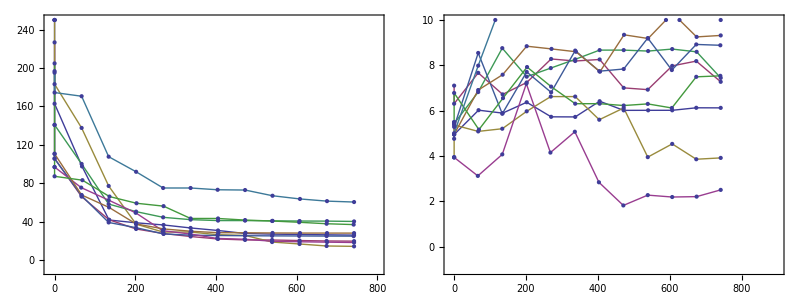

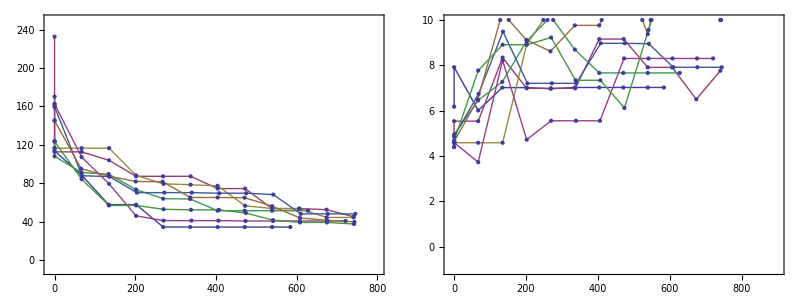

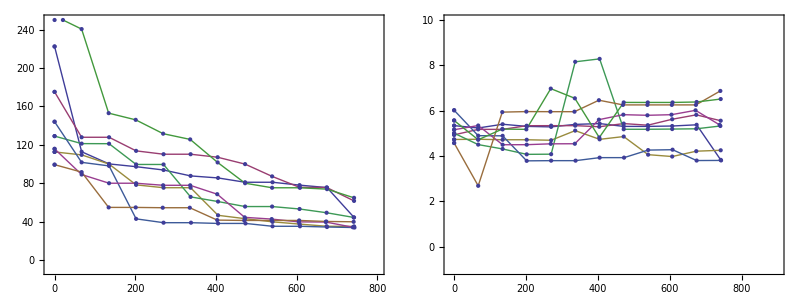

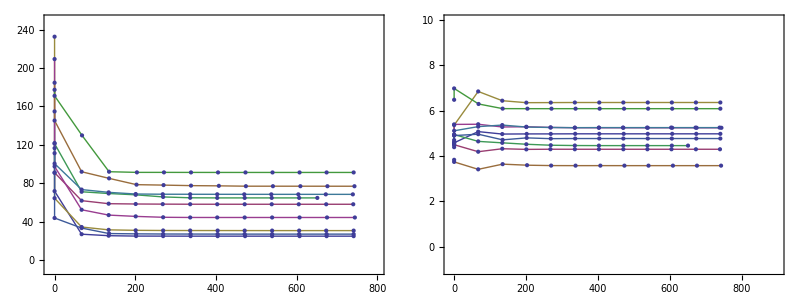

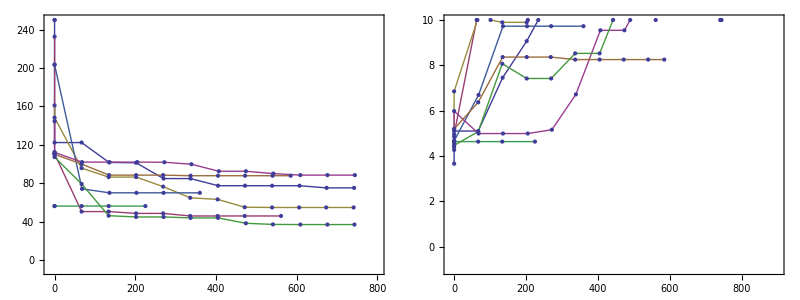

```mathematica
Vi[Import/@FN["met/*m2*bin_*.dev"],P⟦2⟧]
Vi[Import/@FN["met/*m2*bint*.dev"],P⟦2⟧]
Vi[Import/@FN["met/*m2*expt*.dev"],P⟦2⟧]
Vi[Import/@FN["met/*m2*exp_*.dev"],P⟦2⟧]
Vi[Import/@FN["met/*m2*simple*.dev"],P⟦2⟧]
```

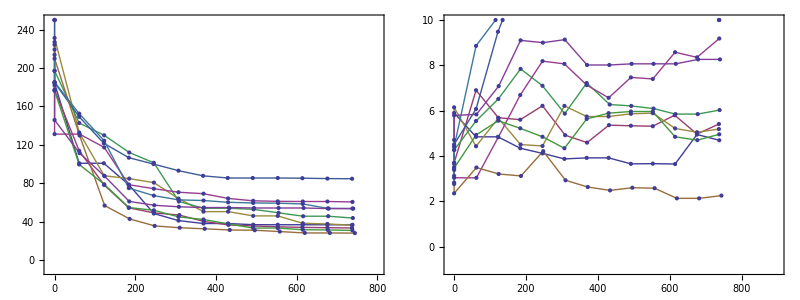

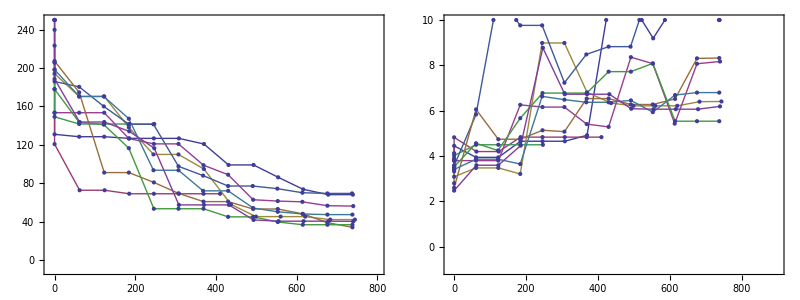

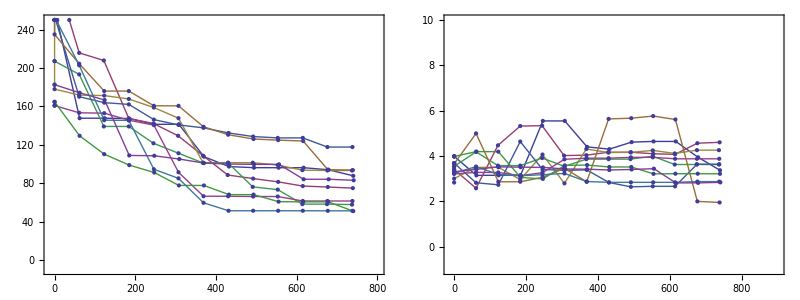

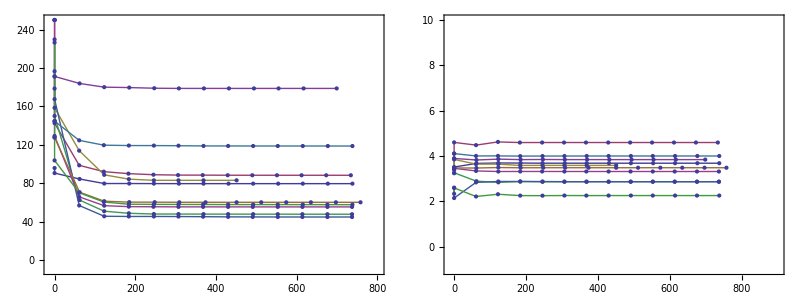

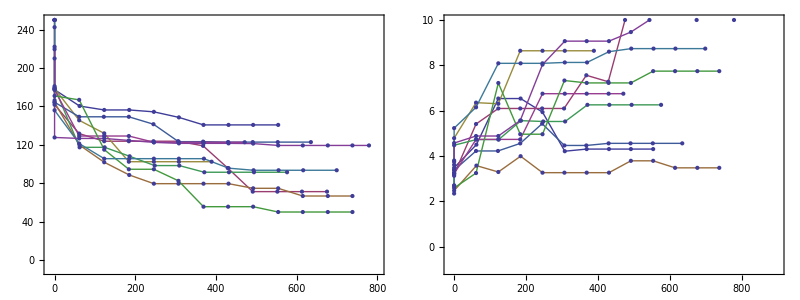

```mathematica
Vi[Import/@FN["met/*m1*bin_*.dev"],P⟦1⟧]
Vi[Import/@FN["met/*m1*bint*.dev"],P⟦1⟧]
Vi[Import/@FN["met/*m1*expt*.dev"],P⟦1⟧]
Vi[Import/@FN["met/*m1*exp_*.dev"],P⟦1⟧]
Vi[Import/@FN["met/*m1*simple*.dev"],P⟦1⟧]
```

#### Размер популяции: 70, 140, 350.

```mathematica
Vi[Import/@FN["psize/*m1p70*.dev"],P⟦1⟧]
Vi[Import/@FN["psize/*m1p140*.dev"],P⟦1⟧]
Vi[Import/@FN["psize/*m1p350*.dev"],P⟦1⟧]
```

```mathematica
Vi[Import/@FN["psize/*m2p70*.dev"],P⟦2⟧]
Vi[Import/@FN["psize/*m2p140*.dev"],P⟦2⟧]
Vi[Import/@FN["psize/*m2p350*.dev"],P⟦2⟧]
```

```mathematica
Vi[Import/@FN["psize/*m3p70*.dev"],P⟦3⟧]
Vi[Import/@FN["psize/*m3p140*.dev"],P⟦3⟧]
Vi[Import/@FN["psize/*m3p350*.dev"],P⟦3⟧]
```